# polya-neumann-balls.nb

## Scripts for the paper “Pólya’s conjecture for higher-dimensional Neumann balls”

by Nikolay Filonov, Michael Levitin, Iosif Polterovich, David A. Sher

## Contents

The sections appear in a slightly different order to those in the paper

```mathematica
Column[{Button["Programming extras",FrontEndExecute[NotebookLocate["Programming extras"]]],
Button["§3. Large λ",FrontEndExecute[NotebookLocate["§3. Large lambda"]]],
Button["§4. Small λ",FrontEndExecute[NotebookLocate["§4. Small lambda"]]],
Button["§2.3. An illustration of main results",FrontEndExecute[NotebookLocate["§2.3. An illustration of main results"]]],
Button["§5. Filling the gap",FrontEndExecute[NotebookLocate["§5. Filling the gap"]]],
Button["Appendices",FrontEndExecute[NotebookLocate["Appendices"]]]
}]
```

Programming extras
§3. Large λ
§4. Small λ
§2.3. An illustration of main results
§5. Filling the gap
Appendices

## Programming extras

```mathematica
SetDirectory[NotebookDirectory[]];
clr=ColorData[97,"ColorList"];
<<MaTeX`
SetOptions[MaTeX,"BasePreamble"->{"\\usepackage[lining]{ebgaramond}","\\usepackage{amsmath}","\\usepackage[ebgaramond]{newtxmath}","\\usepackage{bm}"}, FontSize->12,Magnification->1];
```

```mathematica
?CenteredInterval
LUBounds[expr_, eps_]:=Information[CenteredInterval[expr,eps], "Bounds"];
LBound[expr_, eps_]:=LUBounds[expr,eps][[1]];
UBound[expr_, eps_]:=LUBounds[expr,eps][[2]];
```

## §3. Large λ

### Various definitions and illustrations

Definitions from Proposition 3.3

```mathematica
Subscript[t, 1,0][d_]:=(1+8 d+32 d^2)/(64 d^(5/2));Subscript[t, 1,3][d_]:=If[d<=6,0,-6+d]/(6+24 d); 
Subscript[T, 1][d_,τ_]:=Subscript[t, 1,0][d]+Subscript[t, 1,3][d]τ^(-3);
```

Extra illustration, typical plots of  T_1[d,τ]:

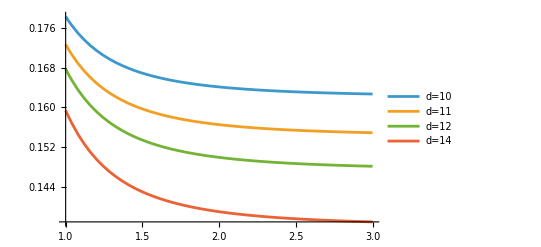

```mathematica
Plot[Table[Subscript[T, 1][d,τ],{d,{10,11,12,14}}]//Evaluate,{τ,1,3},AxesLabel->MaTeX[{"\\tau","\\mathcal{T}_{d,1}(\\tau)"}],PlotLegends->Table["d="<>ToString[d],{d,{10,11,12,14}}]]
```

Definitions from Proposition 3.4

```mathematica
Subscript[t, 2,2]=(3^(2/3) π^(7/6))/(20 2^(5/6));
Subscript[α, 4][d_]:=((3 π)^(2/3) (14 √2-10 √2 d+3 π))/(56 2^(5/6) d);
Subscript[α, 6][d_]:=-((-2+d) π^(4/3) (18-10 d+3 √2 π))/(64 6^(2/3) d^2);
Subscript[α, 8][d_]:=(27 (-3+d) (-2+d) π^2 (-4+√2 π))/(11264 d^3);
```

```mathematica
Subscript[T, 2][d_,τ_]:=Subscript[t, 2,2](τ^(-2)+Subscript[α, 4][d]τ^(-4)+Subscript[α, 6][d]τ^(-6)+Subscript[α, 8][d]τ^(-8));
```

Extra illustration, typical plots of  T_2[d,τ]:

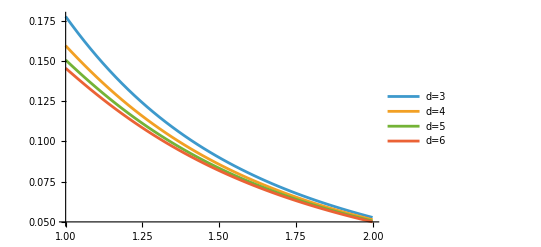

```mathematica
Plot[Table[Subscript[T, 2][d,τ],{d,{3,4,5,6}}]//Evaluate,{τ,1,2},AxesLabel->MaTeX[{"\\tau","\\mathcal{T}_{d,2}(\\tau)"}],PlotLegends->Table["d="<>ToString[d],{d,{3,4,5,6}}]]
```

Definitions from Proposition 3.5

```mathematica
ω=(3 π)^(2/3)/(4 2^(1/3));
Subscript[T, 3][d_,τ_]:=Sqrt[Pi/8] ⅇ^(-ω/τ^2) (1-((-6+d) (-2+d) (-1+d))/(24 d (d τ^3-τ ω)^2)-(d-1)/(2 √d (d τ^3-τ ω)));
```

Extra illustration, typical plots of  T_3[d,τ]:

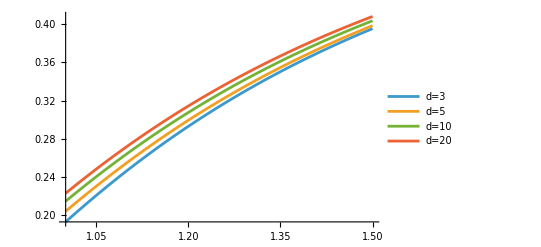

```mathematica
Plot[Table[Subscript[T, 3][d,τ],{d,{3,5,10,20}}]//Evaluate,{τ,1,1.5},AxesLabel->MaTeX[{"\\tau","\\mathcal{T}_{d,3}(\\tau)"}],PlotLegends->Table["d="<>ToString[d],{d,{3,5,10,20}}]]
```

Definition of T_d

```mathematica
T[d_,τ_]:=Subscript[T, 3][d,τ]-Subscript[T, 1][d,τ]-Subscript[T, 2][d,τ];
```

Figure  3

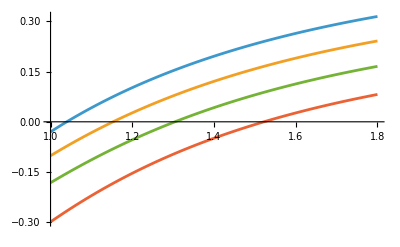

```mathematica
figTdtypical=Plot[{T[30,τ],T[10,τ],T[5,τ],T[3,τ]},{τ,1,1.8},AxesLabel->MaTeX[{"\\tau", "\\mathcal{T}_d(\\tau)"}],PlotLegends->MaTeX[Reverse[{"d=3","d=5","d=10","d=30"}]]]
```

```mathematica
Export["figTdtypical.pdf", figTdtypical]
```

figTdtypical.pdf

### Rational approximations for bounds in Theorem 3.1

Proving that  is negative for d=60 and  positive for d=61

```mathematica
bounds60=LUBounds[T[60,1],10^(-4)]
```

{-44760445596801377675/75557863725914323419136,-29648872838231958923/75557863725914323419136}

```mathematica
bounds61=LUBounds[T[61,1],10^(-4)]
```

{26358269750698667/4722366482869645213696,970831567161287339/4722366482869645213696}

Proving that  is negative for d=12 and positive for d=13

```mathematica
bounds12=LUBounds[T[12,28/25],10^(-3)]
bounds13=LUBounds[T[13,28/25],10^(-3)]
```

{-25931230113289738127/4722366482869645213696,-16486497145626302351/4722366482869645213696}

{7605667427504885135/9444732965739290427392,26495133362831756687/9444732965739290427392}

Numerical values of

```mathematica
τstar=<|Table[d->(SolveValues[{T[d,τ]==0,1<τ<17/10},τ][[1]]//N), {d,3,60}]|>;
TableForm[Table[{d,τstar [d],d+29, τstar [d+29]}, {d,3,31}],TableHeadings->{None,MaTeX[{"d","\\tau_d^*","d","\\tau_d^*"}]}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 1.52217 | 32 | 1.03525
4 | 1.38519 | 33 | 1.03323
5 | 1.30432 | 34 | 1.03131
6 | 1.24964 | 35 | 1.02947
7 | 1.21574 | 36 | 1.02772
8 | 1.18994 | 37 | 1.02605
9 | 1.16954 | 38 | 1.02444
10 | 1.15291 | 39 | 1.02291
11 | 1.13904 | 40 | 1.02143
12 | 1.12727 | 41 | 1.02002
13 | 1.11711 | 42 | 1.01866
14 | 1.10824 | 43 | 1.01734
15 | 1.10041 | 44 | 1.01608
16 | 1.09344 | 45 | 1.01486
17 | 1.08718 | 46 | 1.01369
18 | 1.08152 | 47 | 1.01255
19 | 1.07637 | 48 | 1.01146
20 | 1.07166 | 49 | 1.01039
21 | 1.06733 | 50 | 1.00937
22 | 1.06333 | 51 | 1.00837
23 | 1.05963 | 52 | 1.0074
24 | 1.05618 | 53 | 1.00647
25 | 1.05297 | 54 | 1.00556
26 | 1.04996 | 55 | 1.00468
27 | 1.04714 | 56 | 1.00382
28 | 1.04449 | 57 | 1.00299
29 | 1.04198 | 58 | 1.00217
30 | 1.03962 | 59 | 1.00138
31 | 1.03737 | 60 | 1.00062

## §4. Small λ

### Proposition 4.2 and Remark 4.3

```mathematica
τhash[d_]:=2^(1/3) (1+d)^(1/(3d))Gamma[1+d/2]^(2/(3d))/Sqrt[d];
```

```mathematica
τhash[3]
```

(2 π)^(1/9)/3^(5/18)

```mathematica
LBound[τhash[3]-17/20,10^(-2)]
```

1661057252282206389201/37778931862957161709568

### §4.3. Variational approach: the algorithm

General definitions

```mathematica
Iis[ρ_,d_]:={
Integrate[D[ρ,x]^2 x^(d-1),{x,0,1},Assumptions->d>=3],
Integrate[ρ^2 x^(d-3),{x,0,1},Assumptions->d>=3],
Integrate[ρ^2 x^(d-1),{x,0,1},Assumptions->d>=3]
};
FdOfTau[d_, Iif_, τ_]:=Module[{X,k,λ,Iid},
Iid=Iif[d]//Evaluate;
X = Sqrt[(λ^2 Iid[[3]]-Iid[[1]])/Iid[[2]]+(d/2-1)^2]-(d/2-1);
Sqrt[2Pi](1+1/(4d)) d^(3/2)(X+(d-3)/2)Product[X+k,{k,0,d-3}]/λ^d/.λ->τ^3d^(3/2)
];
```

### §4.4. Constant test function

Integrals

```mathematica
Ii1= Iis[1,d]
Ii1f[d_]:=Evaluate[Ii1];
```

{0,1/(-2+d),1/d}

Figure 4

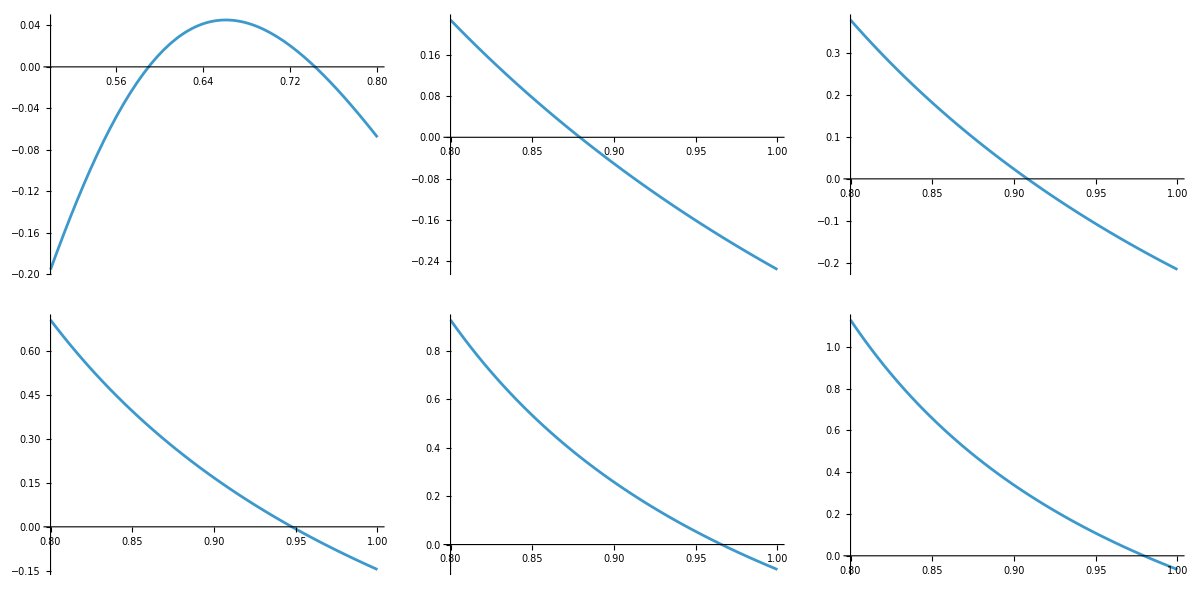

```mathematica
figvar1=Grid[ArrayReshape[
Table[
Plot[FdOfTau[d,Ii1f,τ]-1,{τ,If[d==3,0.5,0.8],If[d==3,0.8,1.0]},ImageSize->Small, PlotLabel->MaTeX["d="<>ToString[d]]],{d,{3,4,5,10,20,50}}],{2,3}]]
```

```mathematica
Export["figvarone.pdf",figvar1]
```

figvarone.pdf

Lower bound for

```mathematica
lowerFd7=(193 (1-1/(d(d-2))) (1+((-2+d) (-1+d))/(8 d^2 τ0^6)) (1-1/(24 τ0^6)-(d-1)/(2 √(-2+d) d τ0^3)))/(77 ⅇ τ0^3)/.{d->7, τ0->17/20}//Simplify
lowerFd7//N
LBound[lowerFd7-1,10^(-2)]
```

-(878684768105600 (-450888949+70747200 √5))/(93387562322467096652199 ⅇ)

1.01312

14751612740489335089/4722366482869645213696

Lower bounds for , d=4, 5, 6

```mathematica
TableForm[Table[Flatten[{d,FdOfTau[d,Ii1f,17/20]//N,LBound[FdOfTau[d,Ii1f,17/20]-1,10^(-2)]}], {d,4,6}],TableHeadings->{None,MaTeX[{"d","\\text{numerical }\\mathfrak{F}_d\\left({\\tau^\\circ}^3 d^{3/2}\\right)","\\text{lower bounds for }\\mathfrak{F}_d\\left({\\tau^\\circ}^3 d^{3/2}\\right)-1\\text{, all positive}"}]}]
```

-Graphics- | -Graphics- | -Graphics-
4 | 1.07694 | 5058082967777020815877/75557863725914323419136
5 | 1.1817 | 25947061976658208927419/151115727451828646838272
6 | 1.24933 | 36165778212213842916809/151115727451828646838272

```mathematica
τcirc = Association[Table[d->τ/.FindRoot[FdOfTau[d,Ii1f,τ]-1, {τ,1}], {d,4,63}]];
```

```mathematica
TableForm[Table[{d,τcirc [d],d+20, τcirc [d+20],d+40, τcirc [d+40] }, {d,4,23}],TableHeadings->{None,MaTeX[{"d","\\tau_d^\\circ","d","\\tau_d^\\circ","d","\\tau_d^\\circ"}]}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | 0.879101 | 24 | 0.969255 | 44 | 0.978072
5 | 0.908255 | 25 | 0.96996 | 45 | 0.97834
6 | 0.922976 | 26 | 0.97062 | 46 | 0.9786
7 | 0.932252 | 27 | 0.97124 | 47 | 0.97885
8 | 0.938794 | 28 | 0.971823 | 48 | 0.979093
9 | 0.943735 | 29 | 0.972373 | 49 | 0.979327
10 | 0.947643 | 30 | 0.972892 | 50 | 0.979554
11 | 0.950836 | 31 | 0.973385 | 51 | 0.979774
12 | 0.953511 | 32 | 0.973852 | 52 | 0.979988
13 | 0.955795 | 33 | 0.974296 | 53 | 0.980194
14 | 0.957776 | 34 | 0.974719 | 54 | 0.980395
15 | 0.959516 | 35 | 0.975122 | 55 | 0.980591
16 | 0.961059 | 36 | 0.975508 | 56 | 0.98078
17 | 0.962442 | 37 | 0.975876 | 57 | 0.980965
18 | 0.963689 | 38 | 0.976229 | 58 | 0.981144
19 | 0.964822 | 39 | 0.976567 | 59 | 0.981319
20 | 0.965858 | 40 | 0.976892 | 60 | 0.981489
21 | 0.966809 | 41 | 0.977204 | 61 | 0.981654
22 | 0.967686 | 42 | 0.977504 | 62 | 0.981816
23 | 0.968499 | 43 | 0.977793 | 63 | 0.981973

### §4.5. Alternative test function

Integrals

```mathematica
ρAlt[d_,x_]:=Piecewise[{{0,0<=x<=1-2/d}},x^((1-d)/2)(x-1+2/d)^(3/2)];
IiAlt=Iis[ρAlt[d,x],d]//Simplify
IiAltf[d_]:=Evaluate[IiAlt];
```

{-(8-88 d+98 d^2-42 d^3+6 d^4+3 (-2+d)^2 d (3-4 d+d^2) Log[(-2+d)/d])/(4 d^3),(-8+18 d-6 d^2-3 (-2+d)^2 d Log[(-2+d)/d])/d^3,4/d^4}

Figure 5

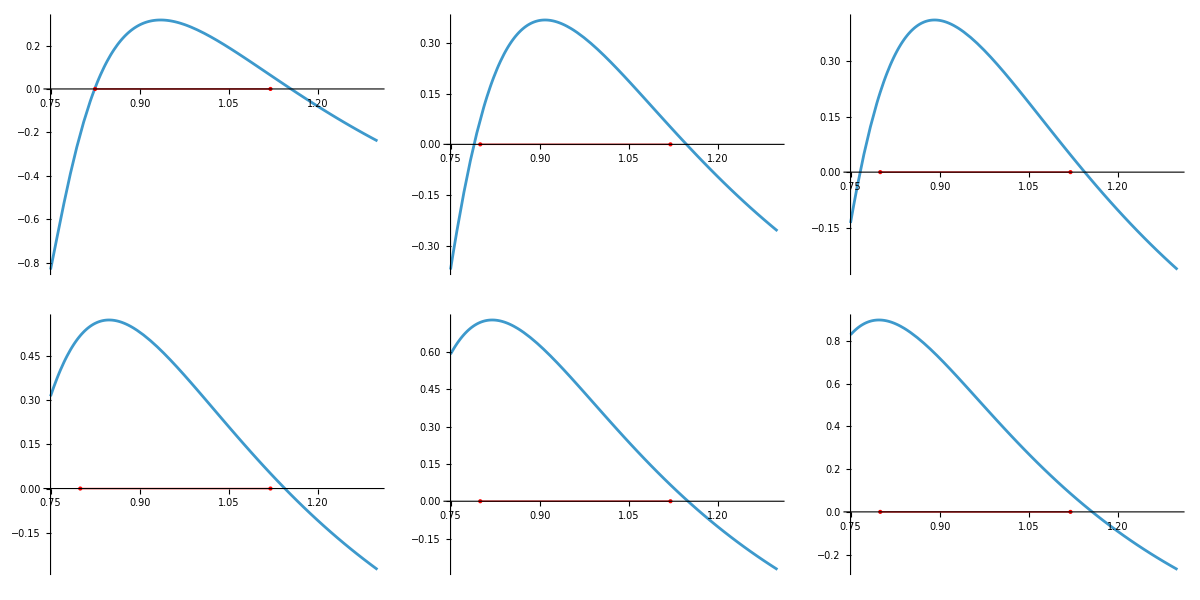

```mathematica
figvarNF=Grid[ArrayReshape[
Table[
Plot[FdOfTau[d,IiAltf,τ]-1,{τ,0.75,1.3},ImageSize->Small, PlotLabel->MaTeX["d="<>ToString[d]],Epilog->{Red,Thick, Line[{{If[d==3,33/40,0.8],0},{1.12,0}}], Point[{If[d==3,{33/40,0},{0.8,0}],{1.12,0}}]}],{d,{3,4,5,10,20,50}}],{2,3}]]
```

```mathematica
Export["figvarNF.pdf",figvarNF]
```

figvarNF.pdf

Case d=3

```mathematica
f31=FdOfTau[3,IiAltf,33/40]//FullSimplify
f31//N
LBound[f31-1,10^(-3)]
```

(832000 √(2 π) (-16000+√(256000000+5991211721/(-8+9 Log[3])))^2)/3759330236558193

1.00521

39743541869798107149/9444732965739290427392

```mathematica
f32=FdOfTau[3,IiAltf,28/25]//FullSimplify
f32//N
LBound[f32-1,10^(-3)]
```

(203125 √(π/2) (-15625+√(244140625+64021110026/(-8+9 Log[3])))^2)/6854839457808384

1.0633

18829485080933663642335/302231454903657293676544

and

```mathematica
τbulletminus= Association[Table[d->τ/.FindRoot[FdOfTau[d,IiAltf,τ]-1, {τ,If[d==3,0.8,0.7]}][[1]], {d,3,62}]];
τbulletplus= Association[Table[d->τ/.FindRoot[FdOfTau[d,IiAltf,τ]-1, {τ,1.2}][[1]], {d,3,62}]];
```

```mathematica
TableForm[Table[{d,τbulletminus[d],τbulletplus[d],d+30, τbulletminus[d+30],τbulletplus[d+30] }, {d,3,32}],TableHeadings->{None,MaTeX[{"d","\\tau_{d,-}^\\bullet","\\tau_{d,+}^\\bullet","d","\\tau_{d,-}^\\bullet","\\tau_{d,+}^\\bullet"}]}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 0.82427 | 1.1545 | 33 | 0.654647 | 1.15355
4 | 0.789579 | 1.14687 | 34 | 0.653783 | 1.15378
5 | 0.766111 | 1.14398 | 35 | 0.652961 | 1.15401
6 | 0.748883 | 1.14303 | 36 | 0.652179 | 1.15422
7 | 0.735612 | 1.14293 | 37 | 0.651433 | 1.15443
8 | 0.725033 | 1.14322 | 38 | 0.650721 | 1.15464
9 | 0.71638 | 1.1437 | 39 | 0.650041 | 1.15483
10 | 0.709155 | 1.14426 | 40 | 0.64939 | 1.15502
11 | 0.703022 | 1.14485 | 41 | 0.648766 | 1.15521
12 | 0.697742 | 1.14544 | 42 | 0.648168 | 1.15539
13 | 0.693144 | 1.14602 | 43 | 0.647594 | 1.15556
14 | 0.689099 | 1.14659 | 44 | 0.647042 | 1.15573
15 | 0.68551 | 1.14713 | 45 | 0.646511 | 1.15589
16 | 0.682301 | 1.14764 | 46 | 0.646 | 1.15605
17 | 0.679412 | 1.14814 | 47 | 0.645508 | 1.15621
18 | 0.676797 | 1.1486 | 48 | 0.645034 | 1.15636
19 | 0.674416 | 1.14905 | 49 | 0.644576 | 1.1565
20 | 0.672239 | 1.14947 | 50 | 0.644134 | 1.15664
21 | 0.670239 | 1.14988 | 51 | 0.643707 | 1.15678
22 | 0.668395 | 1.15026 | 52 | 0.643294 | 1.15692
23 | 0.666688 | 1.15063 | 53 | 0.642894 | 1.15705
24 | 0.665103 | 1.15098 | 54 | 0.642507 | 1.15718
25 | 0.663627 | 1.15132 | 55 | 0.642133 | 1.1573
26 | 0.662248 | 1.15164 | 56 | 0.641769 | 1.15743
27 | 0.660957 | 1.15195 | 57 | 0.641417 | 1.15755
28 | 0.659745 | 1.15224 | 58 | 0.641075 | 1.15766
29 | 0.658606 | 1.15252 | 59 | 0.640743 | 1.15778
30 | 0.657531 | 1.1528 | 60 | 0.640421 | 1.15789
31 | 0.656517 | 1.15306 | 61 | 0.640107 | 1.158
32 | 0.655557 | 1.15331 | 62 | 0.639803 | 1.15811

### Summary of low λ bounds

Figure 6

```mathematica
dmax=15; 
figtotallowpict=ListLinePlot[
{Table[{d,28/25}, {d,3,dmax}], (*1*)
Table[{d,τbulletplus[d]}, {d,3,dmax}],  (*2*)
Table[{d,τhash[d]}, {d,3,dmax}], (*3*)
Table[{d,τcirc[d]}, {d,4,dmax}], (*4*)
Table[{d,17/20}, {d,4,dmax}], (*5*)
Table[{d,τbulletminus[d]}, {d,3,dmax}],  (*6*)
Prepend[Table[{d,4/5}, {d,4,dmax}],{3,τbulletminus[3]}] (*7*)},
PlotMarkers->{
None,
{●, Offset[2]},
{●, Offset[2]} ,
{●, Offset[2]}, 
None,
{●, Offset[2]},
None },
PlotStyle->{
{Black,Thick, Dashed},
{clr[[1]], Thick},
 clr[[2]], 
clr[[3]], 
{clr[[3]], Thick, Dashed},
 clr[[4]],
{clr[[4]], Thick, Dashed}},
PlotLabels->{
MaTeX["\\tau^*=\\tau^\\bullet_+=\\frac{28}{25}"],
MaTeX["\\tau^\\bullet_{d,+}"],
MaTeX["\\tau^\\#_d"],
MaTeX["\\tau^\\circ_d"],
MaTeX["\\tau^\\circ=\\frac{17}{20}"],
MaTeX["\\tau^\\bullet_{d,-}"],
MaTeX["\\tau^\\bullet_{-}=\\frac{4}{5}"]},
Filling->{{3->Axis}, {5->Axis},{7->{1}}},
PlotRange->{{1,dmax}, {0.4,1.25}},
AxesOrigin->{3,0.4},AxesLabel->MaTeX[{"d","\\tau"}],LabelingSize->Full,
Ticks->{3Range[5], Automatic}, ImageSize->Large,GridLines->{Range[dmax-2]+2,None}]
```

-Graphics-

```mathematica
Export["figtotallowpict.pdf",figtotallowpict]
```

figtotallowpict.pdf

## §2.3. An illustration of main results

Figure 1

```mathematica
figtotalpictsmall=ListLinePlot[
{Table[{d,1.6}, {d,3,60}],Table[{d,τstar[d]}, {d,3,60}],Table[{d,28/25}, {d,3,60}]},
PlotMarkers->{None,{●, Offset[2]}, None },
PlotStyle->{None,clr[[1]],{clr[[4]],Thick, Dashed}},
PlotLabels->{None, MaTeX["\\tau^*_d"], MaTeX["\\tau^*=\\frac{28}{25}"]},
Filling->{{2->{1}}, {3->Axis}},
PlotRange->{{0,60}, {0.8,1.6}},
AxesOrigin->{0,0.8},AxesLabel->MaTeX[{"d","\\tau"}],LabelingSize->Full,
Ticks->{5Range[12], Automatic}, ImageSize->Large,GridLines->{Range[58]+2,None}]
```

-Graphics-

```mathematica
Export["figtotalpictsmall.pdf",figtotalpictsmall]
```

figtotalpictsmall.pdf

Enclosures ensuring  that   are upper bounds for

```mathematica
Λstar=<|3->19,4->22,5->25,6->29,7->34,8->39,9->44,10->49,11->54,12->60|>;
```

```mathematica
TableForm[Table[Flatten[{d,τstar[d]^3 d^(3/2),Λstar[d],LBound[T[d,Λstar[d]^(1/3)/Sqrt[d]],10^(-6)]}], {d,3,12}],TableHeadings->{None,MaTeX[{"d","{\\tau^*_d}^3 d^{3/2}","\\Lambda_d^*","\\text{lower bounds for }\\mathcal{T}_d\\left({\\Lambda_d^*}^{1/3}/\\sqrt{d}\\right)\\text{, all positive}"}]}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 18.3261 | 19 | 254172122470243857187875/38685626227668133590597632
4 | 21.2625 | 22 | 260775792285720236271105/38685626227668133590597632
5 | 24.8089 | 25 | 15296388626154291952715/9671406556917033397649408
6 | 28.6799 | 29 | 45126767439274258052623/19342813113834066795298816
7 | 33.2786 | 34 | 178311456678250552577669/38685626227668133590597632
8 | 38.1254 | 39 | 96047214635786503033603/19342813113834066795298816
9 | 43.1923 | 44 | 159448793049023429729303/38685626227668133590597632
10 | 48.4601 | 49 | 48343761363350285852493/19342813113834066795298816
11 | 53.9149 | 54 | 868977098161909352477/2417851639229258349412352
12 | 59.5457 | 60 | 16952017587702127491045/9671406556917033397649408

Figure 2

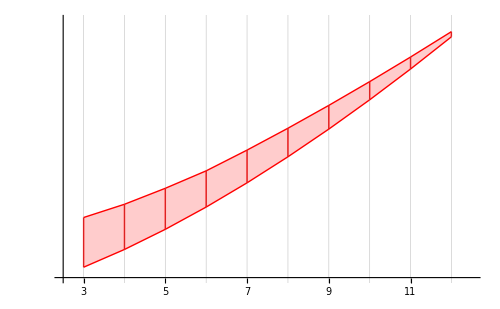

```mathematica
stp=2.5;enp=12.5;
tp= 
Table[{Λstar[d],MaTeX["\\Lambda^*_{"<>ToString[d]<>"}="<>ToString[Λstar[d]]], {(d-stp)/(enp-stp),0},Red}, {d,3,12}];figlambdagap= ListLinePlot[{Table[{d, d^(3/2)τstar[d]^3}, {d,3,12}],Table[{d, d^(3/2)(28/25)^3}, {d,3,12}]},PlotStyle->{{Thick, Red}},PlotRange->{{stp,enp},{5,62}},AxesLabel->MaTeX[{"d","\\lambda"}],
Filling->{1->{2}},Ticks->{Range[10]+2,tp},Epilog->{Thick, Red, Table[Line[{{d,d^(3/2)τstar[d]^3},{d,d^(3/2)(28/25)^3}}],{d,3,12}]},GridLines->{Range[10]+2,None},Ticks->{Automatic,tp},ImageSize->500]
```

```mathematica
Export["figlambdagap1.pdf",figlambdagap]
```

figlambdagap1.pdf

## §5. Filling the gap

### Extra script (should be downloaded to the same folder)

```mathematica
Get["UltrasphericalDerivativeZeros.wl"] (* scripting by Claude *)
```

### A single dimension, reproducing one row of Table 1

```mathematica
listP = ComputeListP[3, 19, 1/100];      (* d = 3, Lambda^*_3 = 19  *)
     Length[listP]                                                    (* K_3 = 50                *)
     NeumannCountingFunction[listP, 3]      (* N^Neu = 570             *)
     PolyaRatio[3, ExpandListP[3, listP]] (* exact; approx 0.9061  *)
     Dataset[ExpandListP[3, listP],ItemDisplayFunction->(Identity[#]&)]  (* the expanded list       *)
```

50

570

1676774056621368167/1850557234384207872

### The full verification of Table 1, d = 3, ..., 12

```mathematica
rows = GapTable[];                         (* prints progress per d   *)
     PolyaCheckPassed[rows]                     (* must be True            *)
     GapTableForm[rows]
     TeXForm[GapTableForm[rows]](* LaTeX source            *)
```

d = 3,  Lambda* = 19,  K_d = 50,  N^Neu = 570,  Polya ratio = 0.906091,  < 1: True

d = 4,  Lambda* = 22,  K_d = 63,  N^Neu = 4701,  Polya ratio = 0.853325,  < 1: True

d = 5,  Lambda* = 25,  K_d = 77,  N^Neu = 36853,  Polya ratio = 0.839623,  < 1: True

d = 6,  Lambda* = 29,  K_d = 101,  N^Neu = 379315,  Polya ratio = 0.768841,  < 1: True

d = 7,  Lambda* = 34,  K_d = 133,  N^Neu = 4307698,  Polya ratio = 0.823,  < 1: True

d = 8,  Lambda* = 39,  K_d = 171,  N^Neu = 49018662,  Polya ratio = 0.751986,  < 1: True

d = 9,  Lambda* = 44,  K_d = 215,  N^Neu = 650176935,  Polya ratio = 0.767317,  < 1: True

d = 10,  Lambda* = 49,  K_d = 262,  N^Neu = 7562155655,  Polya ratio = 0.729007,  < 1: True

d = 11,  Lambda* = 54,  K_d = 314,  N^Neu = 105849911256,  Polya ratio = 0.748369,  < 1: True

d = 12,  Lambda* = 60,  K_d = 386,  N^Neu = 1524056239175,  Polya ratio = 0.701599,  < 1: True

True

d | Λ*_d | K_d | N^Neu | approx. LHS
3 | 19 | 50 | 570 | 0.9061
4 | 22 | 63 | 4701 | 0.8533
5 | 25 | 77 | 36853 | 0.8396
6 | 29 | 101 | 379315 | 0.7688
7 | 34 | 133 | 4307698 | 0.823
8 | 39 | 171 | 49018662 | 0.752
9 | 44 | 215 | 650176935 | 0.7673
10 | 49 | 262 | 7562155655 | 0.729
11 | 54 | 314 | 105849911256 | 0.7484
12 | 60 | 386 | 1524056239175 | 0.7016

\begin{array}{ccccc}
 \text{d} & \text{$\Lambda $*$\_$d} & \text{K$\_$d} & \text{N${}^{\wedge}$Neu} &
   \text{approx. LHS} \\
\hline
 3 & 19 & 50 & 570 & 0.9061 \\
\hline
 4 & 22 & 63 & 4701 & 0.8533 \\
 5 & 25 & 77 & 36853 & 0.8396 \\
 6 & 29 & 101 & 379315 & 0.7688 \\
 7 & 34 & 133 & 4307698 & 0.8230 \\
 8 & 39 & 171 & 49018662 & 0.7520 \\
 9 & 44 & 215 & 650176935 & 0.7673 \\
 10 & 49 & 262 & 7562155655 & 0.7290 \\
 11 & 54 & 314 & 105849911256 & 0.7484 \\
 12 & 60 & 386 & 1524056239175 & 0.7016 \\
\end{array}

### Optional float cross-check of the enclosures in a given dimension

```mathematica
DiagnosticCompare[5, 25, 1/100];
```

77 zeros certified <= 25.;  N^Neu = 36853;  enclosures consistent with floats: True

## Appendices

### Appendix A

Figure 7

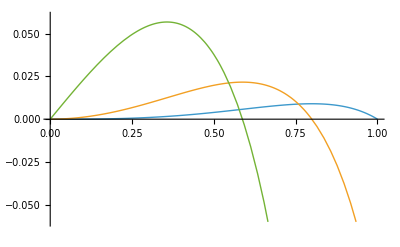

```mathematica
h[t_]:=Sqrt[2]t+(Pi/2-Sqrt[2])t^3-ArcCos[1-t^2];
figphi=Plot[{h[t],h'[t],h''[t]},{t,0.001,1},PlotRange->0.06, PlotStyle->Thick, PlotLegends->MaTeX[{"h(t)","h'(t)","h''(t)"}],AxesLabel->{MaTeX["t"],None}]
```

```mathematica
Export["figphi.pdf",figphi]
```

figphi.pdf

Certified derivative bounds

```mathematica
h30=Limit[h'''[t], t->0, Direction->"FromAbove"]//Simplify;
h11=h'[1]//Simplify;
h21=h''[1]//Simplify;
```

```mathematica
{{MaTeX["h'''(0)"], h30, N[h30],"lower bound: ", LBound[h30,0.1]},
{MaTeX["h'(1)"], h11, N[h11],"upper bound: ",UBound[h11,0.1]},
{MaTeX["h''(1)"], h21, N[h21],"upper bound: ",UBound[h21,0.1]}}//TableForm
```

-Graphics- | -13/(√2)+3 π | 0.23239 | lower bound:  | 312596589495787184215/2361183241434822606848
-Graphics- | -2 (1+√2)+(3 π)/2 | -0.116038 | upper bound:  | -151475989880737737107/9444732965739290427392
-Graphics- | -2-6 √2+3 π | -1.0605 | upper bound:  | -145147172032287534964499/151115727451828646838272

### Appendix C.3

```mathematica
{(81 π^2 (-4+√2 π))/5632,(135 π^2 (-4+√2 π))/11264,(27 π^2 (-4+√2 π))/11264}//Reverse
```

{(27 π^2 (-4+√2 π))/11264,(135 π^2 (-4+√2 π))/11264,(81 π^2 (-4+√2 π))/5632}

Certified bounds

```mathematica
{Subscript[β, 4,0],Subscript[β, 4,1]}={(5 (3 π)^(2/3))/(28 2^(1/3)),((3 π)^(2/3) (14 √2+3 π))/(56 2^(5/6))};
{Subscript[β, 6,0],Subscript[β, 6,1],Subscript[β, 6,2]}={(5 π^(4/3))/(32 6^(2/3)),(π^(4/3) (38+3 √2 π))/(64 6^(2/3)),(3^(1/3) π^(4/3) (6+√2 π))/(32 2^(2/3))};
{Subscript[β, 8,1],Subscript[β, 8,2],Subscript[β, 8,3]}={(27 π^2 (-4+√2 π))/11264,(135 π^2 (-4+√2 π))/11264,(81 π^2 (-4+√2 π))/5632};
 {Subscript[β, 4,0],Subscript[β, 4,1],Subscript[β, 6,0],Subscript[β, 6,1],Subscript[β, 6,2],Subscript[β, 8,1],Subscript[β, 8,2],Subscript[β, 8,3]}//N
```

{0.632387,1.30678,0.21773,1.11758,1.36424,0.0104776,0.0523878,0.0628653}

```mathematica
bdc31=-Subscript[β, 4,0]^2/(3 Subscript[β, 6,0])+1-4/9 Subscript[β, 8,2];
bdc32=(3 Subscript[β, 6,0]-Subscript[β, 6,1])+(2/3 Subscript[β, 4,1]-2 Subscript[β, 4,0])+1-4/9 Subscript[β, 8,2];
bdc33=Subscript[β, 4,1]-Subscript[β, 6,1];
bdc34=Subscript[β, 4,1]-Subscript[β, 6,1]-2/3 Subscript[β, 8,2];
```

```mathematica
TableForm[{
{MaTeX["\\left.\\frac{\\partial\\mathcal{E}(\\sigma, \\xi)}{\\partial\\sigma}\\right|_{\\xi=0}"], MaTeX["-\\frac{\\beta_{4,0}^2}{3 \\beta_{6,0}}+1-\\frac{4}{9}\\beta_{8,2}"],bdc31//N,LBound[bdc31,0.1]},
{MaTeX["\\left.\\frac{\\partial\\mathcal{E}(\\sigma, \\xi)}{\\partial\\sigma}\\right|_{\\xi=\\frac{1}{3}}"], MaTeX[" \\left(3 \\beta_{6,0}-\\beta_{6,1}\\right)+ \\left(\\frac{2 \\beta_{4,1}}{3}-2 \\beta_{4,0}\\right)+1-\\frac{4 \\beta_{8,2}}{9}"],bdc32//N,LBound[bdc32,0.1]},
{MaTeX["\\left.\\frac{\\partial\\mathcal{E}(\\sigma, \\xi)}{\\sigma^2\\partial\\xi}\\right|_{\\xi=0}"], MaTeX["\\beta_{4,1}  - \\beta_{6,1}"],bdc33//N,LBound[bdc33,0.1]},
{MaTeX["\\left.\\frac{\\partial\\mathcal{E}(\\sigma, \\xi)}{\\sigma^2\\partial\\xi}\\right|_{\\xi=\\frac{1}{3}}"], MaTeX["\\beta_{4,1} -\\beta_{6,1} - \\frac{2 \\beta_{8,2}}{3}"],bdc34//N, LBound[bdc34,0.1]}
},TableHeadings->{None, {"expression", "lower bound", "numerical value", "certified bound"}}]
```

expression | lower bound | numerical value | certified bound
-Graphics- | -Graphics- | 0.364472 | 9991456575844081796005/37778931862957161709568
-Graphics- | -Graphics- | 0.118743 | 177025224130477713237/9444732965739290427392
-Graphics- | -Graphics- | 0.189204 | 842505943220936596225/9444732965739290427392
-Graphics- | -Graphics- | 0.154279 | 512647013025024232459/9444732965739290427392

### Appendix C.9

The enclosures for the RHS of (C.21), using (C.18)

```mathematica
tildeQbullet[d_,τ_]:=Sqrt[5d(d-2)/(5d^2-6d-4)-(5 (d-2) (d+8))/(8 d(5 d^2-6 d-4)τ^6)];
RHSC21[d_,τ_]:=193/77 τ^(-3) Exp[-2(d-1)^2/(5d(d-2))]Exp[-(d-1)(d+8)/(2(8d^2 τ^6-d-8))] (1-1/(2τ^3 Sqrt[d] tildeQbullet[d,τ])- 1/(24 τ^6 tildeQbullet[d,τ]^2));
```

```mathematica
TableForm[{{11,4/5,RHSC21[11,4/5]-1//N, LBound[RHSC21[11,4/5]-1,0.01]},
{16,28/25,RHSC21[16,28/25]-1//N, LBound[RHSC21[16,28/25]-1,0.01]}},
TableHeadings->{None, {d,τ, "numerical RHS of (C.21) minus 1", "its certified lower bound"}}]
```

d | τ | numerical RHS of (C.21) minus 1 | its certified lower bound
11 | 4/5 | 0.0816836 | 1354065265920426872099/18889465931478580854784
16 | 28/25 | 0.0113784 | 13018463748926440431/9444732965739290427392

Remaining bounds

```mathematica
TableForm[Table[{d, N[FdOfTau[d,IiAltf,4/5]-1],LBound[FdOfTau[d,IiAltf,4/5]-1,0.01]},{d,4,10}],TableHeadings->{None, {d, MaTeX["\\text{numerical value of }\\mathfrak{F}_d\\left({\\tau_-^\\bullet}^{3}d^{3/2}\\right)-1"],"its certified lower bound"}}]
```

d | -Graphics- | its certified lower bound
4 | 0.0728401 | 296754067571862444971/4722366482869645213696
5 | 0.216595 | 31219678268616387194267/151115727451828646838272
6 | 0.31142 | 91098598266369414583455/302231454903657293676544
7 | 0.38132 | 56112316173282843946877/151115727451828646838272
8 | 0.436132 | 64395206147717355855737/151115727451828646838272
9 | 0.480841 | 71151425572538675004691/151115727451828646838272
10 | 0.518327 | 307264808301731429976683/604462909807314587353088

```mathematica
TableForm[Table[{d, N[FdOfTau[d,IiAltf,28/25]-1],LBound[FdOfTau[d,IiAltf,28/25]-1,0.01]},{d,4,15}],TableHeadings->{None, {d, MaTeX["\\text{numerical value of }\\mathfrak{F}_d\\left({\\tau_+^\\bullet}^{3}d^{3/2}\\right)-1"],"its certified lower bound"}}]
```

d | -Graphics- | its certified lower bound
4 | 0.0510292 | 1550039191747597429469/37778931862957161709568
5 | 0.0468191 | 695493166513223581557/18889465931478580854784
6 | 0.0459553 | 679176454568815477827/18889465931478580854784
7 | 0.0465641 | 690675791309742234145/18889465931478580854784
8 | 0.0478444 | 1429719785363959619767/37778931862957161709568
9 | 0.0494237 | 744692133664820251277/18889465931478580854784
10 | 0.051118 | 1553394496431622870105/37778931862957161709568
11 | 0.0528331 | 1618189803402394099601/37778931862957161709568
12 | 0.0545201 | 1681922480547404124367/37778931862957161709568
13 | 0.056154 | 1743649743456745766967/37778931862957161709568
14 | 0.0577229 | 1802922018977722577177/37778931862957161709568
15 | 0.0592222 | 929781835317065459079/18889465931478580854784